```mathematica
wpe=1;
wpi=1/1836;
v0=1;
```

```mathematica
function[k_,w_]:=1-(wpi*wpi)/(w*w)-(wpe*wpe)/((w-k*v0)*(w-k*v0));
```

```mathematica
(*desenhar as soluções reais da relação de dispersão*)
```

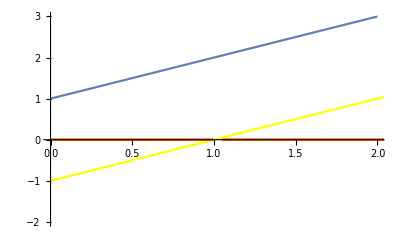

```mathematica
Show [Plot[Re[w/.NSolve[function[k,w]==0,w][[1]]],{k,0,3},PlotRange->{{0,2},{-2,3}}],Plot[Re[w/.NSolve[function[k,w]==0,w][[2]]],{k,0,3},PlotStyle->Yellow],Plot[Re[w/.NSolve[function[k,w]==0,w][[3]]],{k,0,3},PlotStyle->Red],Plot[Re[w/.NSolve[function[k,w]==0,w][[4]]],{k,0,3},PlotStyle->Orange]]
```

```mathematica
(*desenhar as soluções reais da relação de dispersão com zoom para não parecer 0*)
```

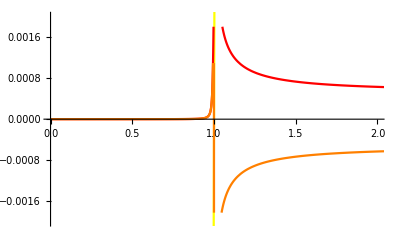

```mathematica
Show [Plot[Re[w/.NSolve[function[k,w]==0,w][[1]]],{k,0,3},PlotRange->{{0,2},{-0.002,0.002}}],Plot[Re[w/.NSolve[function[k,w]==0,w][[2]]],{k,0,3},PlotStyle->Yellow],Plot[Re[w/.NSolve[function[k,w]==0,w][[3]]],{k,0,3},PlotStyle->Red],Plot[Re[w/.NSolve[function[k,w]==0,w][[4]]],{k,0,3},PlotStyle->Orange]]
```

```mathematica
(*desenhar as soluções *)
```

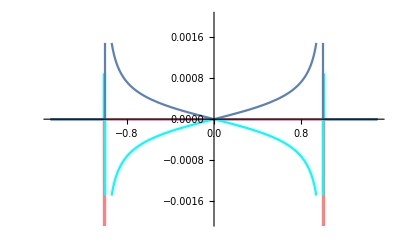

```mathematica
Show [Plot[Im[w/.NSolve[function[k,w]==0,w][[1]]],{k,-1.5,1.5},PlotStyle->Blue,PlotRange->{{-1.5,1.5},{-0.002,0.002}}],Plot[Im[w/.NSolve[function[k,w]==0,w][[2]]],{k,-1.5,1.5},PlotStyle->Pink],Plot[Im[w/.NSolve[function[k,w]==0,w][[3]]],{k,-1.5,1.5},PlotStyle->Cyan],Plot[Im[w/.NSolve[function[k,w]==0,w][[4]]],{k,-1.5,1.5}]]
```

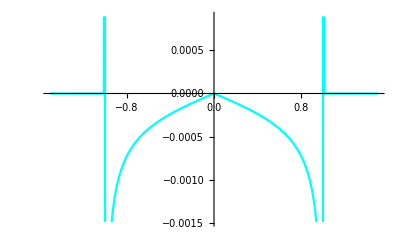

```mathematica
Plot[Im[w/.NSolve[function[k,w]==0,w][[3]]],{k,-1.5,1.5},PlotStyle->Cyan]
```

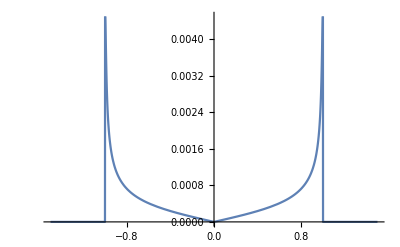

```mathematica
Plot[Im[w/.NSolve[function[k,w]==0,w][[4]]],{k,-1.5,1.5},PlotRange->{{-1.5,1.5}{0,0.003}}]
```

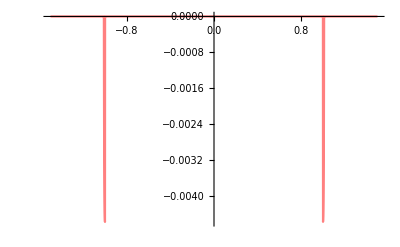

```mathematica
Plot[Im[w/.NSolve[function[k,w]==0,w][[2]]],{k,-1.5,1.5},PlotStyle->Pink]
```

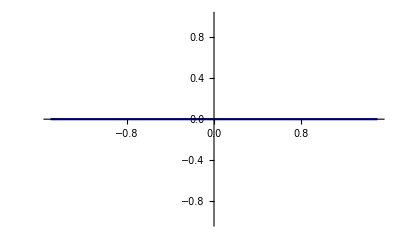

```mathematica
Plot[Im[w/.NSolve[function[k,w]==0,w][[1]]],{k,-1.5,1.5},PlotStyle->Blue]
```

```mathematica
NSolve[{function[k,w]==0,D[function[k,w]==0,w],Im[k]==0},{w,k},WorkingPrecision->10]
```

{{w→-0.006691574378,k→-1.010020718},{w→0.006691574378,k→1.010020718}}

```mathematica
aux=Table[Im[w/.NSolve[{function[k*0.00001,w]==0},{w}][[4]]],{k,90000,100100}];
Position[aux,Max[aux]]
```

{{10005}}

```mathematica
Max[aux]
NumberForm[(90000.+10005.)/100000.]
```

0.00457219

1.00005

```mathematica
wpe=1;
wpi=1/1836;
v0=0.5;
```

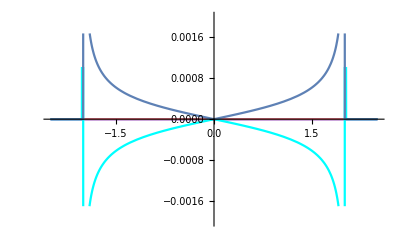

```mathematica
Show [Plot[Im[w/.NSolve[function[k,w]==0,w][[1]]],{k,-2.5,2.5},PlotStyle->Blue,PlotRange->{{-2.5,2.5},{-0.002,0.002}}],Plot[Im[w/.NSolve[function[k,w]==0,w][[2]]],{k,-2.5,2.5},PlotStyle->Pink],Plot[Im[w/.NSolve[function[k,w]==0,w][[3]]],{k,-2.5,2.5},PlotStyle->Cyan],Plot[Im[w/.NSolve[function[k,w]==0,w][[4]]],{k,-2.5,2.5}]]
```

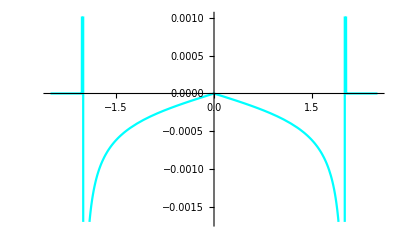

```mathematica
Plot[Im[w/.NSolve[function[k,w]==0,w][[3]]],{k,-2.5,2.5},PlotStyle->Cyan]
```

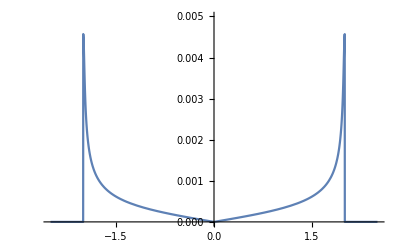

```mathematica
Plot[Im[w/.NSolve[function[k,w]==0,w][[4]]],{k,-2.5,2.5},PlotRange->{{-2.5,2.5},{0,0.005}}]
```

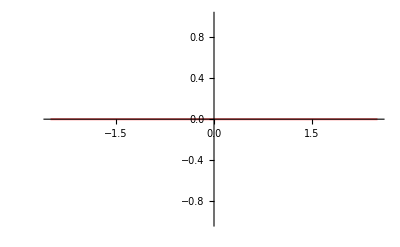

```mathematica
Plot[Im[w/.NSolve[function[k,w]==0,w][[2]]],{k,-2.5,2.5},PlotStyle->Pink]
```

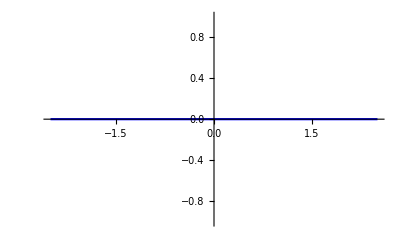

```mathematica
Plot[Im[w/.NSolve[function[k,w]==0,w][[1]]],{k,-2.5,2.5},PlotStyle->Blue]
```

```mathematica
NSolve[{function[k,w]==0,D[function[k,w]==0,w]},{w,k}]
```

{{w→0.00669157,k→2.02004},{w→-0.00669157,k→-2.02004},{w→0.00334584-0.00575658 ⅈ,k→-1.98998-0.0172986 ⅈ},{w→0.00334584+0.00575658 ⅈ,k→-1.98998+0.0172986 ⅈ},{w→-0.00334584-0.00575658 ⅈ,k→1.98998-0.0172986 ⅈ},{w→-0.00334584+0.00575658 ⅈ,k→1.98998+0.0172986 ⅈ}}

```mathematica
aux=Table[Im[w/.NSolve[{function[k*0.0001,w]==0},{w}][[4]]],{k,19000,20200}];
Position[aux,Max[aux]]
Max[aux]
```

{{1001}}

0.00457216

```mathematica
NumberForm[(19000.+1001.)/10000.]
```

2.0001

```mathematica
wpe=1;
wpi=1/1836;
v0=2;
```

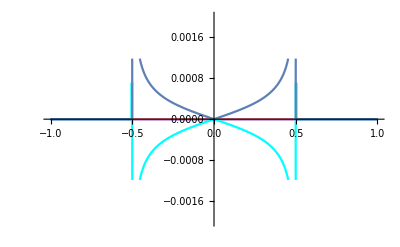

```mathematica
Show [Plot[Im[w/.NSolve[function[k,w]==0,w][[1]]],{k,-1,1},PlotStyle->Blue,PlotRange->{{-1,1},{-0.002,0.002}}],Plot[Im[w/.NSolve[function[k,w]==0,w][[2]]],{k,-1,1},PlotStyle->Pink],Plot[Im[w/.NSolve[function[k,w]==0,w][[3]]],{k,-1,1},PlotStyle->Cyan],Plot[Im[w/.NSolve[function[k,w]==0,w][[4]]],{k,-1,1}]]
```

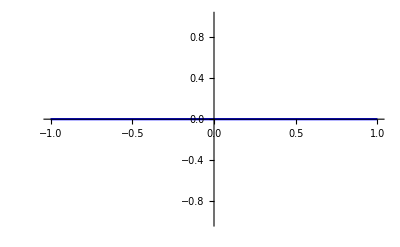

```mathematica
Plot[Im[w/.NSolve[function[k,w]==0,w][[2]]],{k,-1,1},PlotStyle->Blue]
```

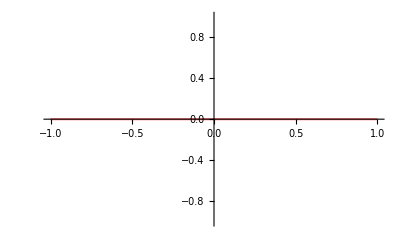

```mathematica
Plot[Im[w/.NSolve[function[k,w]==0,w][[2]]],{k,-1,1},PlotStyle->Pink]
```

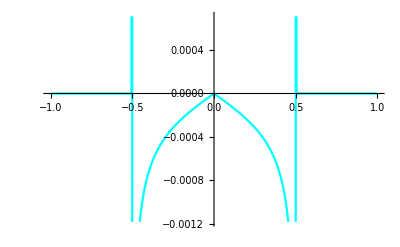

```mathematica
Plot[Im[w/.NSolve[function[k,w]==0,w][[3]]],{k,-1,1},PlotStyle->Cyan]
```

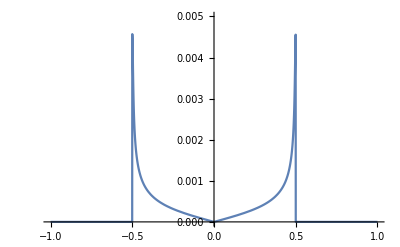

```mathematica
Plot[Im[w/.NSolve[function[k,w]==0,w][[4]]],{k,-1,1},PlotRange->{{-1,1},{0,0.005}}]
```

```mathematica
NSolve[{function[k,w]==0,D[function[k,w]==0,w]},{w,k}]
```

{{w→-0.00669157,k→-0.50501},{w→0.00669157,k→0.50501},{w→-0.00334584-0.00575658 ⅈ,k→0.497495-0.00432466 ⅈ},{w→-0.00334584+0.00575658 ⅈ,k→0.497495+0.00432466 ⅈ},{w→0.00334584-0.00575658 ⅈ,k→-0.497495-0.00432466 ⅈ},{w→0.00334584+0.00575658 ⅈ,k→-0.497495+0.00432466 ⅈ}}

```mathematica
aux=Table[Im[w/.NSolve[{function[k*0.00001,w]==0},{w}][[4]]],{k,45000,50510}];
Position[aux,Max[aux]]
```

{{5003}}

```mathematica
NumberForm[(45000.+5003.)/100000.]
```

0.50003